```mathematica
FullSimplify@Integrate[q^Log[t],{t,1,x}]
```

ConditionalExpression[(-1+q^Log[x] x)/(1+Log[q]),Re[x]≥0||x∉Reals]

```mathematica
Limit[(-1+q^Log[x] x)/(1+Log[q]),q->E^-1]
```

Log[x]

```mathematica
FullSimplify@Integrate[1,{t,1,x}]
```

-1+x

```mathematica
FullSimplify@Integrate[1/t,{t,1,x}]
```

ConditionalExpression[Log[x],Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@Integrate[(q E^-1)^Log[t],{t,1,x}]
```

ConditionalExpression[(-1+q^Log[x])/Log[q],Re[x]≥0||x∉Reals]

```mathematica
(-1+q^Log[x])/Log[q]
```

```mathematica
FullSimplify@Integrate[(q /E)^Log[t],{t,1,x}]
```

ConditionalExpression[(-1+q^Log[x])/Log[q],Re[x]≥0||x∉Reals]

```mathematica
(q /E)^Log[t]
```

q^Log[t]/t

```mathematica
FullSimplify[(-1-Log[q/E])]
```

-Log[q]

```mathematica
FullSimplify[1+Log[q/E]]
```

Log[q]

```mathematica
Integrate[q^t,{t,0,Infinity}]
```

ConditionalExpression[-1/Log[q],Re[Log[q]]<0]

```mathematica
FullSimplify[Log[1/(q/E)]-1]
```

Log[1/q]

```mathematica
FullSimplify[-Log[q/E]]
```

1-Log[q]

```mathematica
FullSimplify[Log[1/(q/E)]-1]
```

Log[1/q]

```mathematica
Expand[1+(1/(Log[1/q]))]/.q->3
```

1-1/Log[3]

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]= Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_,q_]:=Sum[q^Log[j]dz[j,z],{j,1,n}]
Dzm[n_,z_,q_]:=Sum[q^Log[j]dz[j,z]/j,{j,1,n}]
```

```mathematica
N@Expand@Dz[100,z,E^-1]
```

1.+2.09515 z+1.53722 z^2+0.478968 z^3+0.0719219 z^4+0.00400029 z^5+0.000108507 z^6

```mathematica
N@Expand@Dzm[100,z,1]
```

1.+2.09515 z+1.53722 z^2+0.478968 z^3+0.0719219 z^4+0.00400029 z^5+0.000108507 z^6

```mathematica
FullSimplify[D[Log[x]^z/Gamma[z+1],x]]
```

Log[x]^(-1+z)/(x Gamma[z])

```mathematica
FullSimplify[D[Log[x]^k/k!,x]]
```

Log[x]^(-1+k)/(x Gamma[k])

```mathematica
Clear[d2,d2h]
d2[n_,0]:=UnitStep[n-1]
d2[n_,k_]:=d2[n,k]=Sum[d2[Floor[n/j],k-1],{j,2,n}]
d2h[n_,0]:=UnitStep[n-1]
d2h[n_,k_]:=d2h[n,k]=Sum[(1/j)d2h[Floor[n/j],k-1],{j,2,n}]
dd2[n_,k_]:=d2[n,k]-d2[n-1,k]
dd2h[n_,k_]:=d2h[n,k]-d2h[n-1,k]
```

```mathematica
Table[dd2[n,2]/n,{n,1,20}]
```

{0,0,0,1/4,0,1/3,0,1/4,1/9,1/5,0,1/3,0,1/7,2/15,3/16,0,2/9,0,1/5}

```mathematica
Table[dd2h[n,2],{n,1,20}]
```

{0,0,0,1/4,0,1/3,0,1/4,1/9,1/5,0,1/3,0,1/7,2/15,3/16,0,2/9,0,1/5}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]= Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
```

```mathematica
pa[n_,z_,i_]:=If[n^(1/i)<2,1,Sum[dz[j,z MoebiusMu[i]/i]pa[n/j^i,z,i+1],{j,1,n^(1/i)}]]
pa2[n_,z_,i_]:=pa2[n,z,i]=If[n^(1/i)<2,1,Sum[dz[j,z MoebiusMu[i]/i]/j pa2[Floor[n/j^i],z,i+1],{j,1,n^(1/i)}]]
```

```mathematica
Expand[pa[100,z,1]]
```

1+25 z+32 z^2+(77 z^3)/6+(35 z^4)/12+(7 z^5)/40+(7 z^6)/720

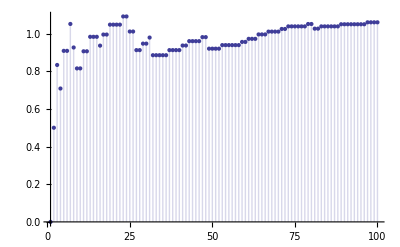

```mathematica
DiscretePlot[D[pa2[n,z,1],z]/.z->0,{n,1,100,1}]
```

```mathematica
Table[D[pa2[n,z,1]-pa2[n-1,z,1],z]/.z->0,{n,1,40}]
```

{0,1/2,1/3,-1/8,1/5,0,1/7,-1/8,-1/9,0,1/11,0,1/13,0,0,-3/64,1/17,0,1/19,0,0,0,1/23,0,-2/25,0,-8/81,0,1/29,0,1/31,-3/32,0,0,0,0,1/37,0,0,0}

```mathematica
Table[pa2[n,1,1]-pa2[n-1,1,1],{n,1,40}]
```

{0,1/2,1/3,0,1/5,1/6,1/7,-1/6,-1/18,1/10,1/11,0,1/13,1/14,1/15,-11/96,1/17,-1/36,1/19,0,1/21,1/22,1/23,-1/18,-3/50,1/26,-7/54,0,1/29,1/30,1/31,-37/320,1/33,1/34,1/35,0,1/37,1/38,1/39,-1/30}

```mathematica
pl[n_]:=FullSimplify@Expand[pa2[n,z,1]-pa2[n-1,z,1]]
```

```mathematica
Table[{Prime[p],pl[Prime[p]],z/Prime[p]},{p,1,10}]//TableForm
```

2 | z/2 | z/2
3 | z/3 | z/3
5 | z/5 | z/5
7 | z/7 | z/7
11 | z/11 | z/11
13 | z/13 | z/13
17 | z/17 | z/17
19 | z/19 | z/19
23 | z/23 | z/23
29 | z/29 | z/29

```mathematica
Table[{Prime[p],pl[Prime[p]^2],1/2/Prime[p]^2 z(z+1-Prime[p])},{p,1,10}]//TableForm
```

2 | 1/8 (-1+z) z | 1/8 (-1+z) z
3 | 1/18 (-2+z) z | 1/18 (-2+z) z
5 | 1/50 (-4+z) z | 1/50 (-4+z) z
7 | 1/98 (-6+z) z | 1/98 (-6+z) z
11 | 1/242 (-10+z) z | 1/242 (-10+z) z
13 | 1/338 (-12+z) z | 1/338 (-12+z) z
17 | 1/578 (-16+z) z | 1/578 (-16+z) z
19 | 1/722 (-18+z) z | 1/722 (-18+z) z
23 | ((-22+z) z)/1058 | ((-22+z) z)/1058
29 | ((-28+z) z)/1682 | ((-28+z) z)/1682

```mathematica
Table[{Prime[p],pl[Prime[p]^3], z(z+1-Prime[p])(z+2-Prime[p])/6/Prime[p]^3},{p,1,10}]//TableForm
```

2 | 1/48 z (-6+(-3+z) z) | 1/48 (-1+z) z^2
3 | 1/162 (-8+z) z (2+z) | 1/162 (-2+z) (-1+z) z
5 | 1/750 z (-48+(-12+z) z) | 1/750 (-4+z) (-3+z) z
7 | (z (-96+(-18+z) z))/2058 | ((-6+z) (-5+z) z)/2058
11 | (z (-240+(-30+z) z))/7986 | ((-10+z) (-9+z) z)/7986
13 | (z (-336+(-36+z) z))/13182 | ((-12+z) (-11+z) z)/13182
17 | (z (-576+(-48+z) z))/29478 | ((-16+z) (-15+z) z)/29478
19 | (z (-720+(-54+z) z))/41154 | ((-18+z) (-17+z) z)/41154
23 | (z (-1056+(-66+z) z))/73002 | ((-22+z) (-21+z) z)/73002
29 | (z (-1680+(-84+z) z))/146334 | ((-28+z) (-27+z) z)/146334

```mathematica
Expand[(z (-96+(-18+z) z))/2058]
```

-(16 z)/343-(3 z^2)/343+z^3/2058

```mathematica
Table[{Prime[p],(D[pl[Prime[p]],z]/.z->0)1 Prime[p]^1,1},{p,1,10}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1
11 | 1 | 1
13 | 1 | 1
17 | 1 | 1
19 | 1 | 1
23 | 1 | 1
29 | 1 | 1

```mathematica
Table[{Prime[p],-(D[pl[Prime[p]^2],z]/.z->0)2Prime[p]^2/(Prime[p]-1),1},{p,1,10}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1
11 | 1 | 1
13 | 1 | 1
17 | 1 | 1
19 | 1 | 1
23 | 1 | 1
29 | 1 | 1

```mathematica
Table[{Prime[p],-(D[pl[Prime[p]^3],z]/.z->0)3Prime[p]^3/(Prime[p]^2-1),1},{p,1,10}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1
11 | 1 | 1
13 | 1 | 1
17 | 1 | 1
19 | 1 | 1
23 | 1 | 1
29 | 1 | 1

```mathematica
Table[{Prime[p],-(D[pl[Prime[p]^4],z]/.z->0)4Prime[p]^4/(Prime[p]^2-1),1},{p,1,7}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1
11 | 1 | 1
13 | 1 | 1
17 | 1 | 1

```mathematica
Table[{Prime[p],-(D[pl[Prime[p]^5],z]/.z->0)5Prime[p]^5/(Prime[p]^4-1),1},{p,1,5}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1
11 | 1 | 1

```mathematica
Table[{Prime[p],(D[pl[Prime[p]^5],z]/.z->0),-(Prime[p]^4-1)/5/Prime[p]^5},{p,1,5}]//TableForm
```

2 | -3/32 | -3/32
3 | -16/243 | -16/243
5 | -624/15625 | -624/15625
7 | -480/16807 | -480/16807
11 | -2928/161051 | -2928/161051

```mathematica
Table[{Prime[p],(D[pl[Prime[p]^6],z]/.z->0)6 Prime[p]^6/(Prime[p]^2-1)/((Prime[p]-1)Prime[p]^2-1),1},{p,1,4}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
5 | 1 | 1
7 | 1 | 1

```mathematica
((7-1)(7)^2-1)
```

293

```mathematica
Expand[6 Prime[p]^6/(Prime[p]^2-1)/((Prime[p]-1)Prime[p]^2-1)]/.Prime[p]->p
```

(6 p^6)/((-1+p^2) (-1+(-1+p) p^2))

```mathematica
Table[{Prime[p],(D[pl[Prime[p]^6],z]/.z->0),(Prime[p]^2-1)((Prime[p]-1)Prime[p]^2-1)/(6 Prime[p]^6)},{p,1,4}]//TableForm
```

2 | 3/128 | 3/128
3 | 68/2187 | 68/2187
5 | 396/15625 | 396/15625
7 | 2344/117649 | 2344/117649

```mathematica
Expand[(Prime[p]^2-1)((Prime[p]-1)Prime[p]^2-1)/(6 Prime[p]^6)]
```

1/(6 Prime[p]^6)-1/(6 Prime[p]^3)-1/(6 Prime[p]^2)+1/(6 Prime[p])

```mathematica
Table[{Prime[p],(D[pl[Prime[p]^4],z]/.z->0),-(Prime[p]^2-1)/(4Prime[p]^4)},{p,1,7}]//TableForm
```

2 | -3/64 | -3/64
3 | -2/81 | -2/81
5 | -6/625 | -6/625
7 | -12/2401 | -12/2401
11 | -30/14641 | -30/14641
13 | -42/28561 | -42/28561
17 | -72/83521 | -72/83521

```mathematica
Expand[-(Prime[p]^2-1)/(4Prime[p]^4)]
```

1/(4 Prime[p]^4)-1/(4 Prime[p]^2)

```mathematica
Table[{Prime[p],(D[pl[Prime[p]^5],z]/.z->0),-(Prime[p]^4-1)/5/Prime[p]^5},{p,1,5}]//TableForm
```

2 | -3/32 | -3/32
3 | -16/243 | -16/243
5 | -624/15625 | -624/15625
7 | -480/16807 | -480/16807
11 | -2928/161051 | -2928/161051

```mathematica
Expand[-(Prime[p]^4-1)/5/Prime[p]^5]
```

1/(5 Prime[p]^5)-1/(5 Prime[p])

```mathematica
Table[{2^p,(D[pl[2^p],z]/.z->0)},{p,1,10}]//TableForm
```

2 | 1/2
4 | -1/8
8 | -1/8
16 | -3/64
32 | -3/32
64 | 3/128
128 | -9/128
256 | -15/2048
512 | -7/512
1024 | 45/2048

```mathematica
Table[{2^p,(D[pl[3^p],z]/.z->0)},{p,1,10}]//TableForm
```

2 | 1/3
4 | -1/9
8 | -8/81
16 | -2/81
32 | -16/243
64 | 68/2187
128 | -104/2187
256 | -10/6561
512 | -728/177147
1024 | 1288/59049

```mathematica
Expand[(1/6)Sum[MoebiusMu[j]/Prime[p]^(6/j),{j,Divisors[6]}]]
```

1/(6 Prime[p]^6)-1/(6 Prime[p]^3)-1/(6 Prime[p]^2)+1/(6 Prime[p])

```mathematica
Expand[(1/5)Sum[MoebiusMu[j]/Prime[p]^(5/j),{j,Divisors[5]}]]
```

1/(5 Prime[p]^5)-1/(5 Prime[p])

```mathematica
Expand[(1/4)Sum[MoebiusMu[j]/Prime[p]^(4/j),{j,Divisors[4]}]]
```

1/(4 Prime[p]^4)-1/(4 Prime[p]^2)

```mathematica
ez[n_]:=Sum[1/p[[2]]Sum[MoebiusMu[j]/(p[[1]]^(p[[2]]/j)),{j,Divisors[p[[2]]]}],{p,FI[n]}]
```

```mathematica
ez[1652]
```

115/3304

```mathematica
pl[1652]
```

((-1+z) z^3)/3304

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]= Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
Dzh[n_,z_]:=Sum[dz[j,z]/j,{j,1,n}]
```

```mathematica
N@Sum[(D[Dzh[100000^(1/k),z],z]/.z->0)MoebiusMu[k]/k,{k,1,Log2@100000}]
```

1.03377

```mathematica
pa[n_,z_,i_]:=If[n^(1/i)<2,1,Sum[dz[j,z MoebiusMu[i]/i]pa[n/j^i,z,i+1],{j,1,n^(1/i)}]]
pa2[n_,z_,i_]:=pa2[n,z,i]=If[n^(1/i)<2,1,Sum[dz[j,z MoebiusMu[i]/i]/j pa2[Floor[n/j^i],z,i+1],{j,1,n^(1/i)}]]
```

```mathematica
DiscretePlot[D[pa2[n,z,1],z]/.z->0,{n,1,100}]
```

-Graphics-

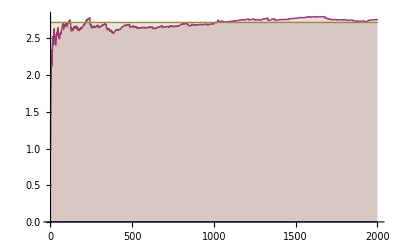

```mathematica
DiscretePlot[{0,pa2[n,1,1],E},{n,1,2000}]
```

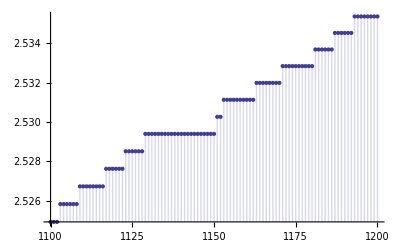

```mathematica
DiscretePlot[D[Dzh[n,z],z]/.z->0,{n,1100,1200}]
```

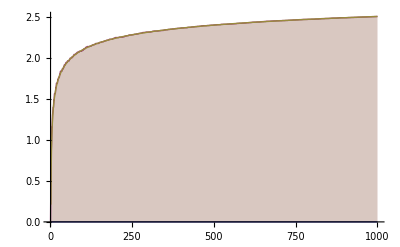

```mathematica
DiscretePlot[{0,D[Dzh[n,z],z]/.z->0,EulerGamma+Log[Log[n]]},{n,1,1000}]
```

```mathematica
Table[FullSimplify[pa2[n,z,1]-pa2[n-1,z,1]],{n,1,10}]//TableForm
```

0
z/2
z/3
1/8 (-1+z) z
z/5
z^2/6
z/7
1/48 z (-6+(-3+z) z)
1/18 (-2+z) z
z^2/10